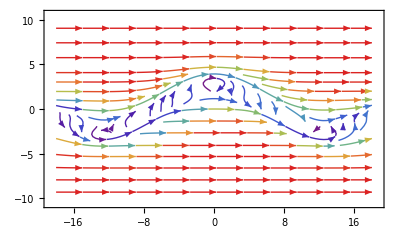

{{{10.0007,7.5734×10^-8},{10.0012,1.42781×10^-7},{10.0019,2.65535×10^-7},95,{9.99911,-2.65535×10^-7},{9.99945,-1.42781×10^-7},{9.99967,-7.5734×10^-8}},{1},97,{1},{1}}
 |  |  |  |

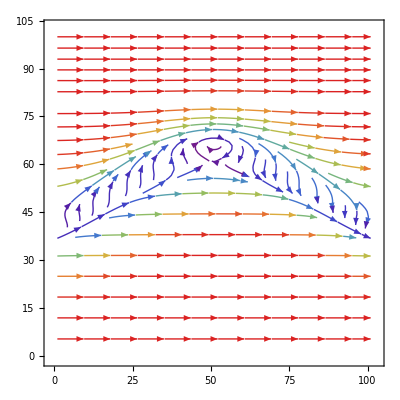

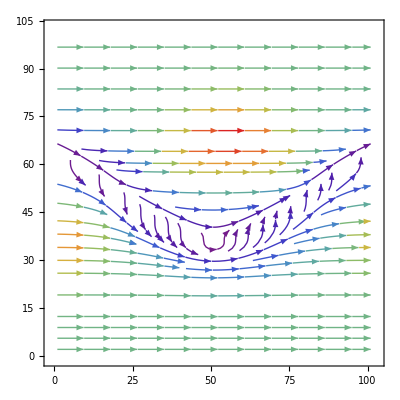

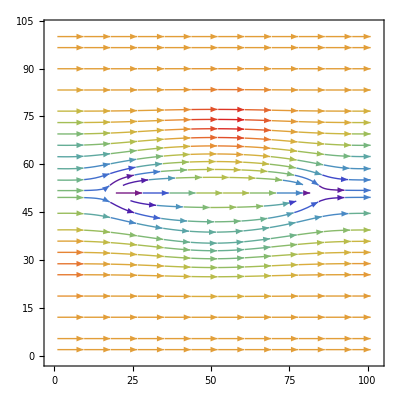

```mathematica
(*Quit
Remove["Global'*"]
clearAll*)

(*StreamPlot[{(y-0.5 Cos[x/4]) Cos[x/4],-Sin[x/4]},{x,-12,12},{y,-10,10},StreamColorFunction->"Rainbow",AspectRatio->Automatic]

Needs["VectorFieldPlots`"]
GradientFieldPlot[-x*(t-5),{x,-10,10},{t,-10,10}]

Quiet[ListVectorPlot[Table[{-y/(x^2+y^2),x/(x^2+y^2)},{x,-3,3,1},{y,-3,3,1}]/.Indeterminate->0]]


]



ListVectorPlot[Table[{y/(x^2+y^2+2),-(x/(x^2+y^2+2))},{x,-3,3,0.3},{y,-3,3,0.3}]]*)

dy=3;flow=5;sv=6;
StreamPlot[{(y-dy Cos[x/4]) Exp[-(y-dy Cos[x/4])^2/sv] Cos[x/4]+flow (1-Exp[-(y-dy Cos[x/4])^2/sv]),-Sin[x/4] Exp[-(y-dy Cos[x/sv])^2/6]},{x,-18,18},{y,-10,10},StreamColorFunction->"Rainbow",AspectRatio->Automatic]

data1=Table[{(y-dy Cos[x/4]) Exp[-(y-dy Cos[x/4])^2/sv] Cos[x/4]+flow (1-Exp[-(y-dy Cos[x/4])^2/sv]),-Sin[x/4] Exp[-(y-dy Cos[x/sv])^2/6]},{x,-10,10,.2},{y,-10,10,.2}];
data2 = Table[{(y+dy Cos[x/4]) Exp[-(y-dy Cos[x/4])^2/sv] Cos[x/4]+flow (1-Exp[-(y+dy Cos[x/4])^2/sv]),Sin[x/4] Exp[-(y+dy Cos[x/sv])^2/6]},{x,-10,10,.2},{y,-10,10,.2}];
data3 = data1 + data2
ListStreamPlot[data1,StreamColorFunction->"Rainbow",AspectRatio->Automatic]
ListStreamPlot[data2,StreamColorFunction->"Rainbow",AspectRatio->Automatic]
ListStreamPlot[data3,StreamColorFunction->"Rainbow",AspectRatio->Automatic]
```